### free β - decay

```mathematica
Clear[me,mp,mn,dm,ddm,E0,σ,tf]
```

```mathematica
me=511 10^3;
mp=938.271 10^6;
mn=939.565 10^6;
dm=mn-mp;
ddm=dm-me;
E0=782 10^3;
```

```mathematica
t[e_]:=E0/(dm-me-e);t[e]
```

E0/(dm-e-me)

```mathematica
mnu[t_]:=Sqrt[8σ]π Sqrt[tf-t];mnu[t[e]]
```

2 √2 π √(-E0/(dm-e-me)+tf) √σ

```mathematica
sigtfsol=Solve[{mnu[t[0]]==mnu0,mnu[t[E0]]==mnuE0},{tf,σ}][[1]]//Factor
```

{σ→0.0000162166 (1. mnu0^2-1. mnuE0^2),tf→(782. (1. mnu0^2-0.00127714 mnuE0^2))/(1. mnu0^2-1. mnuE0^2)}

```mathematica
{σ,tf}/.sigtfsol/.{mnuE0->2,mnu0->ddm}
```

{9.94219×10^6,782.}

```mathematica
m[e_]:=mnu[t[t[e]]]/.sigtfsol;m[e]
```

0.0357828 √(1. mnu0^2-1. mnuE0^2) √(-782000/(783000.-782000/(783000.-e))+(782. (1. mnu0^2-0.00127714 mnuE0^2))/(1. mnu0^2-1. mnuE0^2))

```mathematica
m0=e/.Solve[m[e]==0,e][[1]]/.{mnuE0->2,mnu0->ddm}
```

782999.

```mathematica
E0
```

782000

```mathematica
dm-me
```

783000.

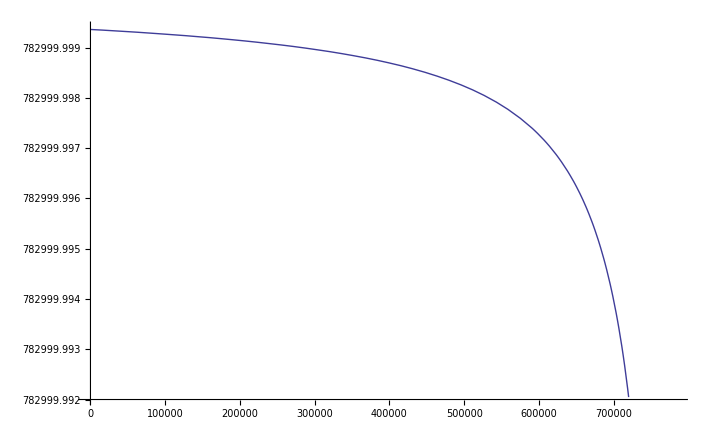

```mathematica
Plot[m[e]/.{mnuE0->2,mnu0->ddm},{e,0, m0}]
```

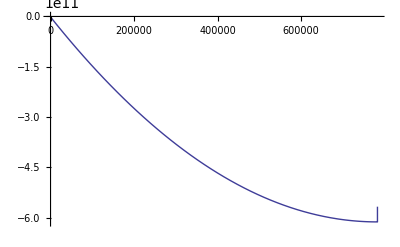

```mathematica
Plot[(E0-e)^2-m[e]^2/.{mnuE0->2,mnu0->ddm},{e,0,m0}]
```

```mathematica
{t[0],t[E0]}
```

{0.998723,782.}